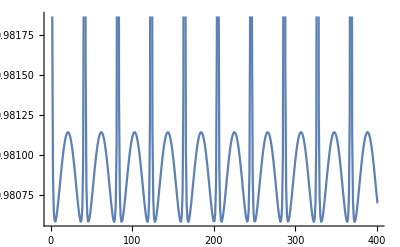

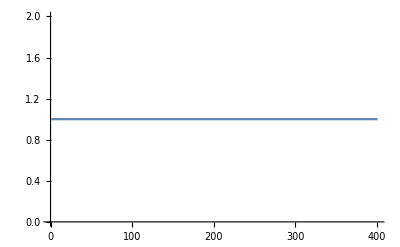

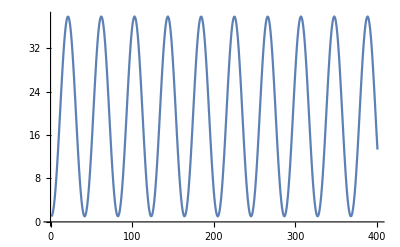

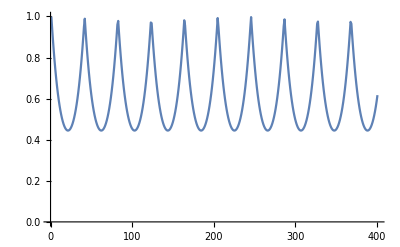

-Graphics-

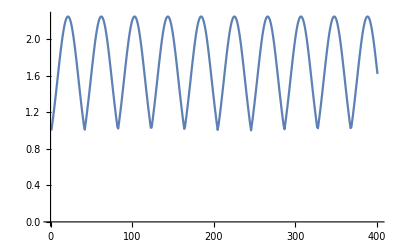

```mathematica
(*X=10 Y=2*)
ListPlot[Table[Eigs[[1]],{t,0,2π,π/200}],Joined->True]
ListPlot[Table[Eigs[[2]],{t,0,2π,π/200}],Joined->True]
ListPlot[Table[Eigs[[3]],{t,0,2π,π/200}],Joined->True]
ListPlot[Table[Eigs[[4]],{t,0,2π,π/200}],Joined->True]
ListPlot[Table[Eigs[[5]],{t,0,2π,π/200}],Joined->True]
ListPlot[Table[Eigs[[6]],{t,0,2π,π/200}],Joined->True]
(*Checking first condition for Bona Fide C.M.; These eigenfunctions should be greater than 0 to be physical*)
```

```mathematica
EigSymp=Eigenvalues[σ+ⅈ Σ];
ListPlot[Table[EigSymp[[1]],{t,0,2π,π/100}],Joined->True]
ListPlot[Table[EigSymp[[2]],{t,0,2π,π/100}],Joined->True]
ListPlot[Table[EigSymp[[3]],{t,0,2π,π/100}],Joined->True]
ListPlot[Table[EigSymp[[4]],{t,0,2π,π/100}],Joined->True]
ListPlot[Table[EigSymp[[5]],{t,0,2π,π/100}],Joined->True]
ListPlot[Table[EigSymp[[6]],{t,0,2π,π/100}],Joined->True]
(*Checking second condition for Bona Fide C.M.; These eigenfunctions should be also greater than 0 to be physical*)
(*NOT PLOTTING*)
```

Throw::sysexc: Uncaught SystemException returned to top level. Can be caught with Catch[…, _SystemException].

$Aborted

```mathematica
SympEig=Eigenvalues[ⅈ Σ . σ];
ListPlot[Table[Abs[SympEig[[1]]],{t,0,2π,π/200}],Joined->True,PlotRange->{0,Automatic}]
ListPlot[Table[Abs[SympEig[[2]]],{t,0,2π,π/200}],Joined->True,PlotRange->{0,Automatic}]
ListPlot[Table[Abs[SympEig[[3]]],{t,0,2π,π/200}],Joined->True,PlotRange->{0,Automatic}]
ListPlot[Table[Abs[SympEig[[4]]],{t,0,2π,π/200}],Joined->True,PlotRange->{0,Automatic}]
ListPlot[Table[Abs[SympEig[[5]]],{t,0,2π,π/200}],Joined->True,PlotRange->{0,Automatic}]
ListPlot[Table[Abs[SympEig[[6]]],{t,0,2π,π/200}],Joined->True,PlotRange->{0,Automatic}]
(*Checking third condition for Bona Fide C.M.; These eigenfunctions should be also greater than or equal 1 (not zero) to be physical*)
```

N::meprec: Internal precision limit $MaxExtraPrecision = 50. reached while evaluating Root[-14956176870719582442288495701896326286102500673401441484800 Cos[1/25 Power[«2»] π]^6+«21»+(-13886862112560513024-102713477163909120000 Cos[«1»]^2+213644032500930969600 Cos[«1»]^3-132541470932308328448 Cos[«1»]^4-94496398990796390400 Sin[«1»]^2+213644032500930969600 Cos[Times[«3»]] Sin[«1»]^2-265082941864616656896 Cos[«1»]^2 Sin[«1»]^2-132541470932308328448 Sin[«1»]^4) #1^2+#1^3&,1].

$Aborted

```mathematica
V1=Table[Min[Abs[Eigenvalues[ⅈ Σ . σPT1]]],{t,0,2π,π/200}];
V2=Table[Min[Abs[Eigenvalues[ⅈ Σ . σPT2]]],{t,0,2π,π/200}];
V3=Table[Min[Abs[Eigenvalues[ⅈ Σ . σPT3]]],{t,0,2π,π/200}];
(*Symplectic eigenvalues. If any are less than 1 then there exists some entanglement: NPT criterion*)
```

```mathematica
ListPlot[Table[V1,{t,0,2π,π/200}],Joined->True,PlotRange->{0,Automatic}]
ListPlot[Table[V2,{t,0,2π,π/200}],Joined->True,PlotRange->{0,Automatic}]
ListPlot[Table[V3,{t,0,2π,π/200}],Joined->True,PlotRange->{0,Automatic}]
```

$Aborted

```mathematica
LogNeg1=Table[Max[0,-Log[Min[Abs[Eigenvalues[ⅈ Σ . σPT1]]]]],{t,0,2π,π/200}];
LogNeg2=Table[Max[0,-Log[Min[Abs[Eigenvalues[ⅈ Σ . σPT2]]]]],{t,0,2π,π/200}];
LogNeg3=Table[Max[0,-Log[Min[Abs[Eigenvalues[ⅈ Σ . σPT3]]]]],{t,0,2π,π/200}];
```

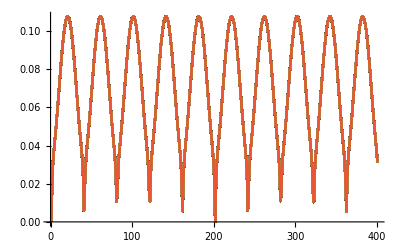

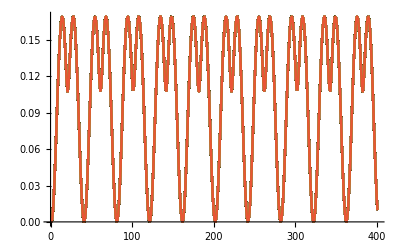

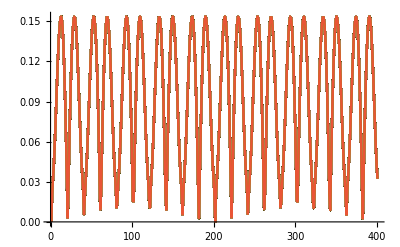

```mathematica
ListPlot[Table[LogNeg1,{t,0,2π,π/200}],Joined->True,PlotRange->{0,Automatic}]
ListPlot[Table[LogNeg2,{t,0,2π,π/200}],Joined->True,PlotRange->{0,Automatic}]
ListPlot[Table[LogNeg3,{t,0,2π,π/200}],Joined->True,PlotRange->{0,Automatic}]
```

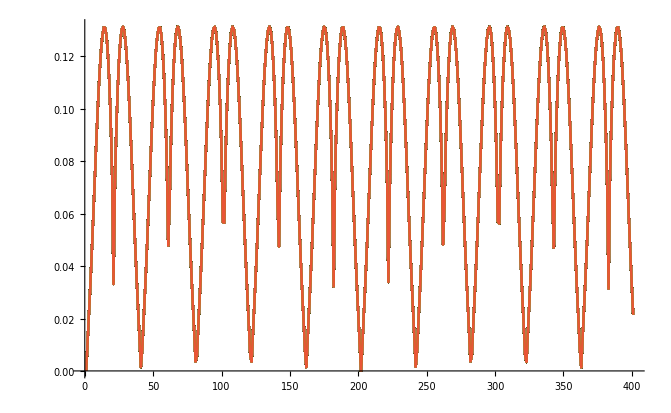

```mathematica
LogNeg123=Table[CubeRoot[(Max[0,-Log[Min[Abs[Eigenvalues[ⅈ Σ . σPT1]]]]])(Max[0,-Log[Min[Abs[Eigenvalues[ⅈ Σ . σPT2]]]]])(Max[0,-Log[Min[Abs[Eigenvalues[ⅈ Σ . σPT3]]]]])],{t,0,2π,π/200}]//Chop;
ListPlot[Table[LogNeg123,{t,0,2π,π/200}],Joined->True,PlotRange->{0,Automatic}]
```